```mathematica
spectralist1=Import["./Denver/fullspectra2018"<>ToString[1]<>".mx"];
spectralist2=Import["./Denver/fullspectra2018"<>ToString[2]<>".mx"];
spectralist3=Import["./Denver/fullspectra2018"<>ToString[3]<>".mx"];
spectralist4=Import["./Denver/fullspectra2018"<>ToString[4]<>".mx"];
spectralist5=Import["./Denver/fullspectra2018"<>ToString[5]<>".mx"];
spectralist6=Import["./Denver/fullspectra2018"<>ToString[6]<>".mx"];
spectralist7=Import["./Denver/fullspectra2018"<>ToString[7]<>".mx"];
spectralist8=Import["./Denver/fullspectra2018"<>ToString[8]<>".mx"];
spectralist9=Import["./Denver/fullspectra2018"<>ToString[9]<>".mx"];
spectralist10=Import["./Denver/fullspectra2018"<>ToString[10]<>".mx"];
spectralist11=Import["./Denver/fullspectra2018"<>ToString[11]<>".mx"];
spectralist12=Import["./Denver/fullspectra2018"<>ToString[12]<>".mx"];
```

```mathematica
(*LSC orientation; vector defining its surface normal in degrees*)
lscAltitude=90 ;(*0 is vertical, 90 is horizontal*)
lscAzimuth = 180;(*0 is facing North, 180 is facing South*)

sphericaltoCartesian[θ_,ϕ_]=FromSphericalCoordinates[{1,π/180.(90.-θ),-π+2π /360.ϕ}];(*shifted to our angle definition: normal definition is theta from 0 to pi, phi from -pi to pi*)

normDot[a_,b_]:=a.b/(Norm[a]Norm[b]);(*normed dotproduct to calculate the angle between sun angle and surface normal*)

realAngleAtLSC[ θ_,ϕ_] := (*effective angle between lsc and sun, we can do this since the lsc is symmetric in the plane*)
Module[{a, b},
a = sphericaltoCartesian[lscAltitude,lscAzimuth];
b =sphericaltoCartesian[θ,ϕ];(*this is the orientation of the surface normal of the LSC*)
90(*go from surface normal angle to surface angle*)- ArcCos[normDot[a, b]]360./(2π)
  ];
```

```mathematica
getmeangles[data_]:= Module[{angles1,times1},
angles1 = data[[;;,{2,-1}]];
angles1 =realAngleAtLSC[#[[1]],#[[2]]]&/@angles1;
times1=data[[;;,1]];
times1 = DateString[#]&/@times1;
Return[Transpose[{times1,angles1}]];
]
```

```mathematica
jan = getmeangles[spectralist1];
feb = getmeangles[spectralist2];
mar = getmeangles[spectralist3];
april = getmeangles[spectralist4];
may = getmeangles[spectralist5];
june = getmeangles[spectralist6];
july = getmeangles[spectralist7];
aug = getmeangles[spectralist8];
sept = getmeangles[spectralist9];
oct = getmeangles[spectralist10];
nov = getmeangles[spectralist11];
dec = getmeangles[spectralist12];
year=Join[jan,feb,mar,april,may,june,july,aug,sept,oct,nov,dec];
```

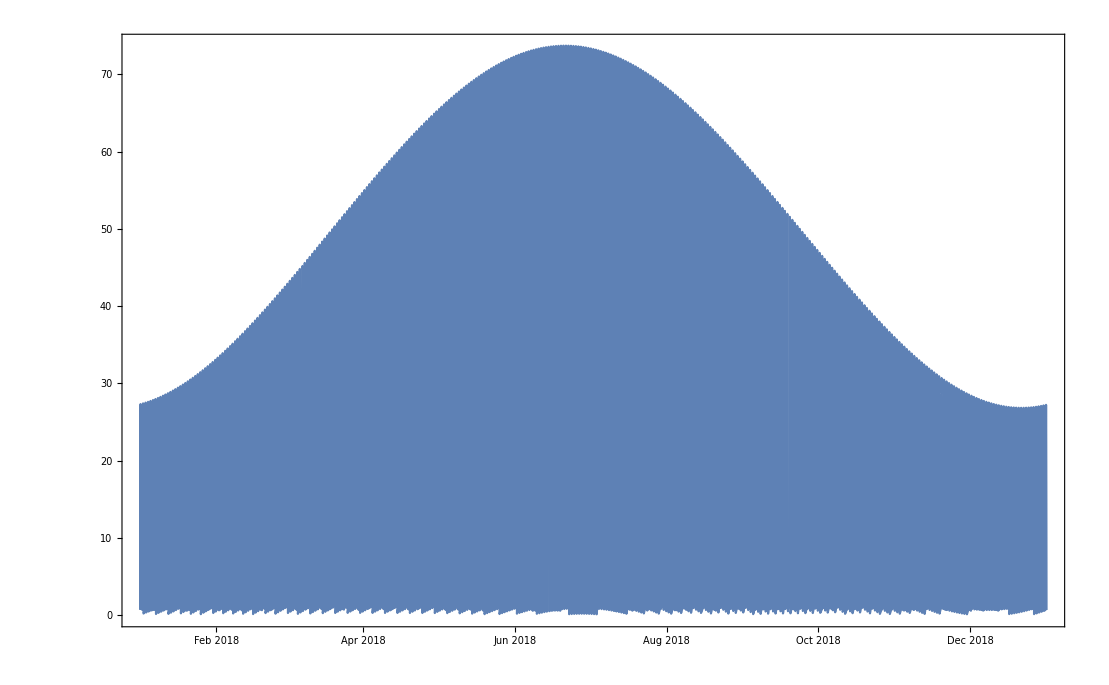

```mathematica
DateListPlot[year]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Export["./plots_for_sanity_colorado/directangles.csv",year]
```

./plots_for_sanity_colorado/directangles.csv